## Chimp&See

```mathematica
rawData=Import["/Users/katjad/Documents/CitizenScienceData/Chimp+See - Sheet1.csv"][[3;;-1;;2]];
```

FunctionRepository`$cb2edf2c655749de9e1c90cb79dff58a`ColorBrewerData::subsamplecolorscheme: Color scheme RdBu has as least 3 colors, subsampling will be used to get 2 color(s).

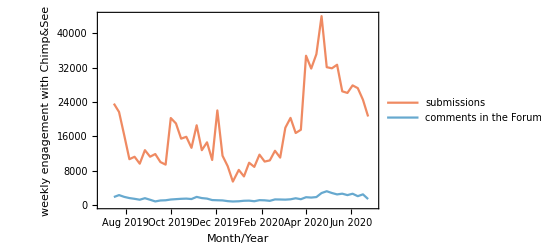

```mathematica
DateListPlot[{Join[{DateObject[{2019,1,1}]+Quantity[7,"Days"]*(#[[1]]-1),#[[2]]}&/@rawData/.""->Missing[],{DateObject[{2020,1,1}]+Quantity[7,"Days"]*(#[[1]]-1),#[[4]]}&/@rawData/.""->Missing[]],Join[{DateObject[{2019,1,1}]+Quantity[7,"Days"]*(#[[1]]-1),#[[3]]}&/@rawData/.""->Missing[],{DateObject[{2020,1,1}]+Quantity[7,"Days"]*(#[[1]]-1),#[[5]]}&/@rawData/.""->Missing[]]},Frame->True,FrameLabel->{"Month/Year","weekly engagement with Chimp&See"},PlotLegends->{"submissions","comments in the Forum"},PlotTheme->{"LargeLabels"},PlotStyle->ResourceFunction["ColorBrewerData"]["RdBu",2],PlotRange->{{DateObject[{2019,07,01}],DateObject[{2020,07,01}]},All},DateTicksFormat->{"MonthShort","/","YearShort"}]
```

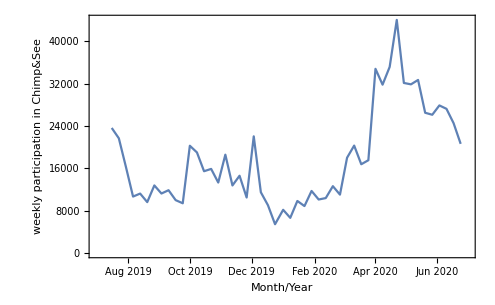

```mathematica
DateListPlot[Join[{DateObject[{2019,1,1}]+Quantity[7,"Days"]*(#[[1]]-1),#[[2]]}&/@rawData/.""->Missing[],{DateObject[{2020,1,1}]+Quantity[7,"Days"]*(#[[1]]-1),#[[4]]}&/@rawData/.""->Missing[]],Frame->True,FrameLabel->{"Month/Year","weekly participation in Chimp&See"},PlotTheme->{"LargeLabels"},PlotRange->{{DateObject[{2019,07,01}],DateObject[{2020,07,01}]},All},DateTicksFormat->{"MonthShort","/","YearShort"}]
```

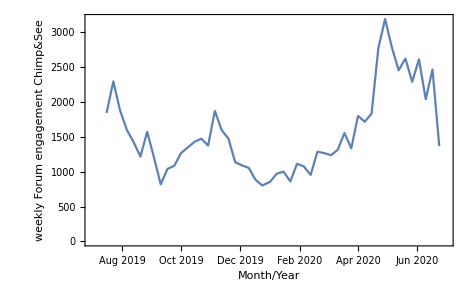

```mathematica
DateListPlot[Join[{DateObject[{2019,1,1}]+Quantity[7,"Days"]*(#[[1]]-1),#[[3]]}&/@rawData/.""->Missing[],{DateObject[{2020,1,1}]+Quantity[7,"Days"]*(#[[1]]-1),#[[5]]}&/@rawData/.""->Missing[]],Frame->True,FrameLabel->{"Month/Year","weekly Forum engagement Chimp&See"},PlotTheme->{"LargeLabels"},PlotRange->{{DateObject[{2019,07,01}],DateObject[{2020,07,01}]},All},DateTicksFormat->{"MonthShort","/","YearShort"}]
```

```mathematica
},
```

```mathematica
subData=<|2019->Association[#[[1]]->#[[2]]&/@rawData],2020->Association[#[[1]]->#[[4]]&/@rawData]|>/.""->Missing[];
talkData=<|2019->Association[#[[1]]->#[[3]]&/@rawData],2020->Association[#[[1]]->#[[5]]&/@rawData]|>/.""->Missing[];
```

```mathematica
subData
```

<|2019→<|1→Missing[],2→Missing[],3→Missing[],4→Missing[],5→Missing[],6→Missing[],7→Missing[],8→Missing[],9→Missing[],10→Missing[],11→Missing[],12→Missing[],13→Missing[],14→Missing[],15→1971,16→741,17→1404,18→1550,19→836,20→Missing[],21→Missing[],22→Missing[],23→Missing[],24→Missing[],25→Missing[],26→Missing[],27→Missing[],28→Missing[],29→23627,30→21671,31→16253,32→10668,33→11233,34→9621,35→12772,36→11244,37→11869,38→9996,39→9403,40→20265,41→19003,42→15455,43→15891,44→13317,45→18581,46→12767,47→14602,48→10488,49→22042,50→11482,51→9036,52→5447|>,2020→<|1→8167,2→6649,3→9838,4→8875,5→11727,6→10113,7→10385,8→12629,9→11036,10→18006,11→20297,12→16771,13→17534,14→34793,15→31801,16→35155,17→44029,18→32123,19→31862,20→32690,21→26494,22→26119,23→27879,24→27238,25→24534,26→20625,27→Missing[],28→Missing[],29→Missing[],30→Missing[],31→Missing[],32→Missing[],33→Missing[],34→Missing[],35→Missing[],36→Missing[],37→Missing[],38→Missing[],39→Missing[],40→Missing[],41→Missing[],42→Missing[],43→Missing[],44→Missing[],45→Missing[],46→Missing[],47→Missing[],48→Missing[],49→Missing[],50→Missing[],51→Missing[],52→Missing[]|>|>

FunctionRepository`$cb2edf2c655749de9e1c90cb79dff58a`ColorBrewerData::subsamplecolorscheme: Color scheme RdBu has as least 3 colors, subsampling will be used to get 2 color(s).

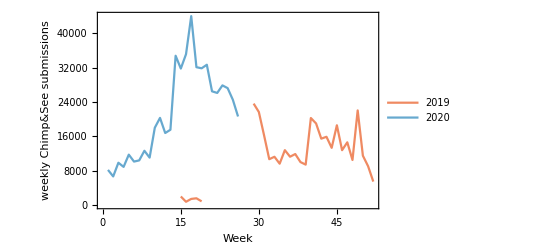

```mathematica
ListLinePlot[Lookup[#,Range[1,52]]&/@Lookup[subData,Range[2019,2020],<||>],Frame->True,FrameLabel->{"Week","weekly Chimp&See submissions"},PlotLegends->{"2019","2020"},PlotTheme->{"LargeLabels"},PlotStyle->ResourceFunction["ColorBrewerData"]["RdBu",2],PlotRange->All]
```

```mathematica
Lookup[#,Range[1,52]]&/@Lookup[Map[Total,GroupBy[(#[[1]][[2]]&)->Last]/@GroupBy[Normal[submitterCountsByWeek],#[[1]][[1]]&],{2}]]
```

```mathematica
Grid[rawData,Frame->All]
```

| 2019 Sub | 2019 Talk | 2020 Sub | 2020 Talk
1 |  |  | 8167 | 855
2 |  |  | 6649 | 973
3 |  |  | 9838 | 1001
4 |  |  | 8875 | 862
5 |  |  | 11727 | 1115
6 |  |  | 10113 | 1076
7 |  |  | 10385 | 955
8 |  |  | 12629 | 1288
9 |  |  | 11036 | 1268
10 |  |  | 18006 | 1238
11 |  |  | 20297 | 1315
12 |  |  | 16771 | 1557
13 |  |  | 17534 | 1337
14 |  |  | 34793 | 1801
15 | 1971 |  | 31801 | 1719
16 | 741 |  | 35155 | 1835
17 | 1404 |  | 44029 | 2774
18 | 1550 |  | 32123 | 3193
19 | 836 |  | 31862 | 2784
20 |  |  | 32690 | 2457
21 |  |  | 26494 | 2625
22 |  |  | 26119 | 2292
23 |  |  | 27879 | 2614
24 |  |  | 27238 | 2042
25 |  |  | 24534 | 2469
26 |  |  | 20625 | 1369
27 |  |  |  | 
28 |  |  |  | 
29 | 23627 | 1843 |  | 
30 | 21671 | 2297 |  | 
31 | 16253 | 1880 |  | 
32 | 10668 | 1601 |  | 
33 | 11233 | 1425 |  | 
34 | 9621 | 1218 |  | 
35 | 12772 | 1573 |  | 
36 | 11244 | 1208 |  | 
37 | 11869 | 820 |  | 
38 | 9996 | 1041 |  | 
39 | 9403 | 1086 |  | 
40 | 20265 | 1268 |  | 
41 | 19003 | 1350 |  | 
42 | 15455 | 1430 |  | 
43 | 15891 | 1475 |  | 
44 | 13317 | 1376 |  | 
45 | 18581 | 1874 |  | 
46 | 12767 | 1598 |  | 
47 | 14602 | 1477 |  | 
48 | 10488 | 1137 |  | 
49 | 22042 | 1092 |  | 
50 | 11482 | 1056 |  | 
51 | 9036 | 886 |  | 
52 | 5447 | 804 |  |